```mathematica
(* constants*)
(*https://en.wikipedia.org/wiki/Avogadro_constant*)
N0=6.02214076*10^23;
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
mev=0.510998928;
(*single monopole charge*)
Qm=2*Pi*hbar/e;
(*http://en.wikipedia.org/wiki/Fine-structure_constant*)
α=1/137.035999206;
αw=0.42541281596347497;
(*From:https://en.wikipedia.org/wiki/Fermi%27s_interaction*)
Gf=1.4327038609285911*^-49;
Ω=0.0078749969978123844;
kb=1.380658*10^(-16);
omega=0.00787499699;
mH=126*10^3*me/mev;
mp=1.672621777*10^(-24);
mn=1838.6402*me;
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
θwrad=ArcSin[Sqrt[0.231208]];
θwdeg=θwrad*180/Pi;
(*https://en.wikipedia.org/wiki/Precision_tests_of_QED*)
g=2*1.00115965218085;
(* unification mass:anti-deSitter model*)
muni=3.6543166832631125*^-12;
mtau=1776.82*me/mev;
mmu=105.6583715*me/mev;
mpi=139.57018*me/mev;
mhiggs=126*10^3*me/mev;
mz=91.1876*10^3*me/mev;
mw=80.4335*10^3*me/mev;
mtop=172.76*10^3*me/mev;
mbottom=4.1*10^3*me/mev;
mcharm=1.275*10^3*me/mev;
mstrange=92.4*me/mev;
momegassb=6054.4/10^3;
mplanck=Sqrt[hbar*c/G];
mup=2.01*me/mev;
md0=4.79*me/mev;
(* log linear fit for 4th level quarks*)
mwhite=1.1677931388727855*^-19;
mblack=1.8611487827001873*^-22;
mout=1.5020666505936996*^-20;
Tvac=2.72548;
(*http://en.wikipedia.org/wiki/Observable_universe*)
ru=8.8*10^28/2;
rplanck=2*Pi*hbar/(mplanck*c);
tplanck=rplanck/c;
(*http://en.wikipedia.org/wiki/Big_Bang*)
(*years*days*hours*minutes*seconds*)
tu=13.798*10^9*365.25*24*60*60;
mnu=1.78266270 * 10^(-33 );
mnumu=6.7978246932973695*^-31;
mnutau=1.1431743145263108*^-29;
(*Weak charge on 5d simplex*)
Cw=(3!*2!)*Det[{{α,0,0,0,0,1},{0,α,0,0,0,1},{0,0,α,0,0,1},{0,0,0,α,0,1},{0,0,0,0,α,1},{0,0,0,0,0,1}}]/5!;
rw=Cw^2/(mnu*c^2);
(*http://www.bottomlayer.com/bottom/deutsch/neutrino.html*)
(* Weeks volume*)
vw=0.94270736277692772092;

(* Thurston-Meyerhoff volume*)
vt=0.981368828892232088914;
(*lepton hyperbolic 3 manifold volume*)
vl=(18/24)*vt;
pizero=134.9766*me/mev;
(* Bohr radius: https://en.wikipedia.org/wiki/Bohr_radius*)
ab=5.2917721067*10^(-9);
(*:https://en.wikipedia.org/wiki/Pion:*)
tpip=2.6033*10^(−8 );
tpiz=8.4*10^(−17);
(* product quarks masses in me*)
mup1=12.239779918021176;mdp1=12.256361761325056;
(* elliptic product quarks for Pi mesons*)
mupi=16.25229214603282;mdpi=16.805755043381577;
mqmu=Sqrt[mmu/me];
mqtau=Sqrt[mtau/me];
(* hadron strange and charm product quark masses*)
mqs=mqtau*mup1/mqmu;
mqc=2*mqs;
ttau=2.932*10^(−13);
tmu=2.1969811*10^(−6);
(*.10https://physicstoday.scitation.org/doi/10.1063/PT.3.4424*)
(*.10https://physics.stackexchange.com/questions/134856/units-of-hubble-time-and-hubble-constant*)
Hcbm=67.4/(3.09*10^19);
Hsnova=74.0/(3.09*10^19);
Hlense=73.3/(3.09*10^19);
Have=73.8/(3.09*10^19);
H0=2.2894835758225842*^-18;
th0=1/H0;
(* CMB age*)
tcmb=372000*365.25*24*60*60;
tsnova=1/Hsnova;
msun=1.9891*10^33;
(*first approximation electron g:single loop GED:weak g'*)
g0=2*(1+α/2);
Clear[g1]
g1=g1/.Solve[(g1/Sqrt[g+g1^2])^2==0.231208,g1][[2]];
(* gravity momemt γ*)
γ=e*G/(hbar*c);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(* anomalous magnetic moment of electron:https://en.wikipedia.org/wiki/Anomalous_magnetic_dipole_moment*)
ae=0.0015865218059;
```

```mathematica
(*https://en.wikipedia.org/wiki/Grand_unification_energy#:~:text=The%20grand%20unification%20energy%2C%20or%20the%20GUT%20scale%2C,one%20force%20governed%20by%20a%20simple%20Lie%20group.*)
```

```mathematica
mGUT=10^16*me/mev;
```

```mathematica
Clear[s,x,Phi]
```

```mathematica
s[1]={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
s[2]={{I,0},{0,-I}}
```

{{ⅈ,0},{0,-ⅈ}}

```mathematica
s[3]={{0,-1},{1,0}}
```

{{0,-1},{1,0}}

```mathematica
s[4]={{0,I},{I,0}}
```

{{0,ⅈ},{ⅈ,0}}

```mathematica
m[1]=Sum[s[i],{i,4}]
```

{{1+ⅈ,-1+ⅈ},{1+ⅈ,1-ⅈ}}

```mathematica
guv={{1,0},{0,-1}}
```

{{1,0},{0,-1}}

```mathematica
v={1,-1}
```

{1,-1}

```mathematica
(*electromagnetic field tensor*)
```

```mathematica
(*scale : Weinberg weak angle*)
```

```mathematica
s=θw0
```

0.231208

```mathematica
Fuv=s*(e/Sqrt[r])*m[1].guv
```

{{(2.3622×10^8+2.3622×10^8 ⅈ)/(√(1/m)),(2.3622×10^8-2.3622×10^8 ⅈ)/(√(1/m))},{(2.3622×10^8+2.3622×10^8 ⅈ)/(√(1/m)),-(2.3622×10^8-2.3622×10^8 ⅈ)/(√(1/m))}}

```mathematica
(*emergy -momentum tensor as Ricci tensor :Already Unified SO(4) theory*)
```

```mathematica
r=2*Pi*hbar/(m*c)
```

(2.21022×10^-37)/m

```mathematica
Ruv=Fuv.Transpose[Fuv]/2
```

{{(0.988891+0. ⅈ) m,(0.494445+1.116×10^17 ⅈ) m},{(0.494445+1.116×10^17 ⅈ) m,(0.988891+0. ⅈ) m}}

```mathematica
(* Ricci scalar reduction*)
```

```mathematica
R=v.Ruv.v
```

(0.988891-2.23199×10^17 ⅈ) m

```mathematica
Tuv0=(Ruv-R*guv/2)*c^4/(-8*Pi*G)
```

{{(-2.38159×10^47-5.3754×10^64 ⅈ) m,-4.81669×10^47 ((0.+0. ⅈ)+(0.494445+1.116×10^17 ⅈ) m)},{-4.81669×10^47 ((0.+0. ⅈ)+(0.494445+1.116×10^17 ⅈ) m),(-7.14477×10^47+5.3754×10^64 ⅈ) m}}

```mathematica
Tuv1={{1/2,0},{0,-1/2}}*m*c^2/(4*Pi*r^3/3)
```

{{9.9361×10^129 m^4,0.},{0.,-9.9361×10^129 m^4}}

```mathematica
T0=v.guv.Tuv0.v
```

0.+(4.76318×10^47-1.07508×10^65 ⅈ) m

```mathematica
T1=FullSimplify[Det[Tuv1]^(1/2)]
```

9.9361×10^129 √(-m^8)

```mathematica
m/.NSolve[T0-T1==0,m]
```

{2.21178×10^-22+3.26645×10^-40 ⅈ,1.10589×10^-22+1.91546×10^-22 ⅈ,-1.10589×10^-22+1.91546×10^-22 ⅈ,0.,0.}

```mathematica
w={0.,-(3.7477115552025455 e^(2/3) hbar^(2/3) s^(2/3))/G^(1/3),-((1.8738557776012728+3.245613412861891 ⅈ) e^(2/3) hbar^(2/3) s^(2/3))/G^(1/3),-((1.8738557776012728-3.245613412861891 ⅈ) e^(2/3) hbar^(2/3) s^(2/3))/G^(1/3),((1.8738557776012728-3.245613412861891 ⅈ) e^(2/3) hbar^(2/3) s^(2/3))/G^(1/3),((1.8738557776012728+3.245613412861891 ⅈ) e^(2/3) hbar^(2/3) s^(2/3))/G^(1/3),(3.7477115552025455 e^(2/3) hbar^(2/3) s^(2/3))/G^(1/3)}
```

{0.,-2.21178×10^-22,-1.10589×10^-22-1.91546×10^-22 ⅈ,-1.10589×10^-22+1.91546×10^-22 ⅈ,1.10589×10^-22-1.91546×10^-22 ⅈ,1.10589×10^-22+1.91546×10^-22 ⅈ,2.21178×10^-22}

```mathematica
(*Solve[(3.7477115552025455 e^(2/3) hbar^(2/3) s^(2/3))/G^(1/3)-mhiggs==0,s]*)
```

```mathematica
Abs[w]
```

{0.,2.21178×10^-22,2.21178×10^-22,2.21178×10^-22,2.21178×10^-22,2.21178×10^-22,2.21178×10^-22}

```mathematica
%/mhiggs
```

{0.,0.984696,0.984696,0.984696,0.984696,0.984696,0.984696}

```mathematica
w0=w/(2.211779242611446*^-22)
```

{0.,-1.,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,0.5+0.866025 ⅈ,1.}

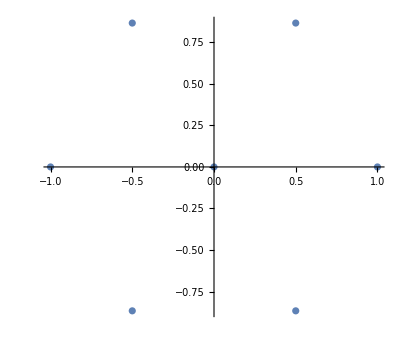

```mathematica
ComplexListPlot[w0]
```

```mathematica
ExpandAll[Product[x-w0[[i]],{i,7}]]//Chop
```

-1. x+x^7

```mathematica
(*end*)
```